```mathematica
ClearAll[ξ,ξξ,δ,f,ϕ,κ];
$Assumptions=ξ≥0&&ξξ≥0&&0<δ≤1;
IFun1=(ξξ-ξ Cos[ϕ])f[ξξ](1/(√(ξ^2+ξξ^2-2ξ ξξ Cos[ϕ]))-δ/(√(ξ^2+ξξ^2-2ξ ξξ Cos[ϕ]+4 κ^2)));
IFun2=f[ξξ]/(√(ξξ^2-f[ξξ]^2));
```

# Little ξ case

```mathematica
FullSimplify[Integrate[Normal[Series[IFun1,{ξ,0,6}]],{ϕ,0,2π}]]
```

1/128 π (256-(256 δ ξξ)/(√(4 κ^2+ξξ^2))+ξ^2 (-64/ξξ^2+(64 δ ξξ (16 κ^2+ξξ^2))/((4 κ^2+ξξ^2)^(5/2)))+ξ^4 (-12/ξξ^4+(12 δ ξξ (-384 κ^4+48 κ^2 ξξ^2+ξξ^4))/((4 κ^2+ξξ^2)^(9/2)))+ξ^6 (-5/ξξ^6+(5 δ ξξ (4096 κ^6-2304 κ^4 ξξ^2+96 κ^2 ξξ^4+ξξ^6))/((4 κ^2+ξξ^2)^(13/2)))) f[ξξ]

```mathematica
FullSimplify[D[%,ξ]]
```

1/8 π ξ (-8/ξξ^2+(8 δ ξξ (16 κ^2+ξξ^2))/((4 κ^2+ξξ^2)^(5/2))+ξ^2 (-3/ξξ^4+(3 δ ξξ (-384 κ^4+48 κ^2 ξξ^2+ξξ^4))/((4 κ^2+ξξ^2)^(9/2)))) f[ξξ]

```mathematica
D[f[ξ]/(ξ √(ξ^2-f[ξ]^2)),ξ]
```

-f[ξ]/(ξ^2 √(ξ^2-f[ξ]^2))+f'[ξ]/(ξ √(ξ^2-f[ξ]^2))-(f[ξ] (2 ξ-2 f[ξ] f'[ξ]))/(2 ξ (ξ^2-f[ξ]^2)^(3/2))

```mathematica
Integrate[(CC x^2)/(√(1+CC^2 x^2))1/x^2,{x,0,Infinity}]
```

∫_0^∞ CC/(√(1+CC^2 x^2))ⅆx

```mathematica
Integrate[1/Sqrt[1+x^2],x]
```

ArcSinh[x]

```mathematica
FullSimplify[Integrate[C/Sqrt[1+C^2 x^2]-δ x^3(x^2+16 κ^2)/(x^2+4 κ^2)^(5/2)/Sqrt[1+C^2 x^2],x]]
```

ArcSinh[C x]+δ ((8 √(1+C^2 x^2) κ^2 (x^2+2 κ^2+8 C^2 κ^4))/((x^2+4 κ^2)^(3/2) (1-4 C^2 κ^2)^2)-Log[C (√(1+C^2 x^2)+C √(x^2+4 κ^2))]/C)

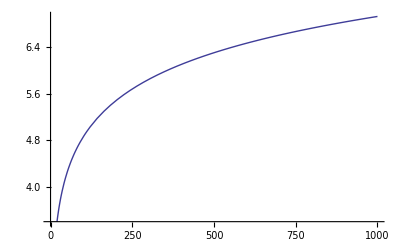

```mathematica
Plot[ArcSinh[x]+ 0.1((8 √(1+x^2)(x^2+2+8))/((x^2+4)^(3/2) (1-4)^2)-Log[(√(1+ x^2)+ √(x^2+4))]),{x,0,1000}]
```

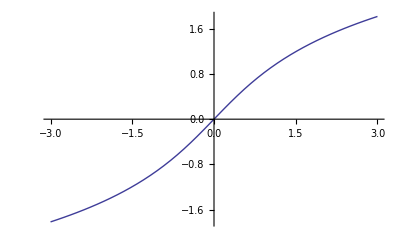

```mathematica
Plot[ArcSinh[x],{x,-3,3}]
```

```mathematica
D[IFun1,ξ]
```

(ξξ-ξ Cos[ϕ]) (-(2 ξ-2 ξξ Cos[ϕ])/(2 (ξ^2+ξξ^2-2 ξ ξξ Cos[ϕ])^(3/2))+(δ (2 ξ-2 ξξ Cos[ϕ]))/(2 (4 κ^2+ξ^2+ξξ^2-2 ξ ξξ Cos[ϕ])^(3/2))) f[ξξ]-Cos[ϕ] (1/(√(ξ^2+ξξ^2-2 ξ ξξ Cos[ϕ]))-δ/(√(4 κ^2+ξ^2+ξξ^2-2 ξ ξξ Cos[ϕ]))) f[ξξ]

## Large ξ case

```mathematica
IFun11=IFun1/.{ξ->1/η}
```

(ξξ-Cos[ϕ]/η) (1/(√(1/η^2+ξξ^2-(2 ξξ Cos[ϕ])/η))-δ/(√(1/η^2+4 κ^2+ξξ^2-(2 ξξ Cos[ϕ])/η))) f[ξξ]

```mathematica
FullSimplify[Integrate[Normal[Series[IFun11,{η,0,2}]],{ϕ,0,2π}]]
```

-π (-1+δ) η ξξ f[ξξ]

## Thick film aproximation

```mathematica
Integrate[((ξξ-ξ Cos[ϕ])f[ξξ])/(√(ξ^2+ξξ^2-2ξ ξξ Cos[ϕ])),{ϕ,0,2π}]
```

ConditionalExpression[1/(√((ξ-ξξ)^2) ξξ √((ξ+ξξ)^2))((ξ-ξξ)^2 √((ξ+ξξ)^2) EllipticE[-(4 ξ ξξ)/(ξ-ξξ)^2]+(ξ+ξξ) (√((ξ-ξξ)^2) (ξ+ξξ) EllipticE[(4 ξ ξξ)/(ξ+ξξ)^2]-(ξ-ξξ) (√((ξ+ξξ)^2) EllipticK[-(4 ξ ξξ)/(ξ-ξξ)^2]+√((ξ-ξξ)^2) EllipticK[(4 ξ ξξ)/(ξ+ξξ)^2]))) f[ξξ],Re[(ξ+ξξ)^2]>0&&Re[(ξ-ξξ)^2]>0]

```mathematica
Assuming[{(ξ+ξξ)^2>0,(ξ-ξξ)^2>0},FullSimplify[1/(√((ξ-ξξ)^2) ξξ √((ξ+ξξ)^2))((ξ-ξξ)^2 √((ξ+ξξ)^2) EllipticE[-(4 ξ ξξ)/(ξ-ξξ)^2]+(ξ+ξξ) (√((ξ-ξξ)^2) (ξ+ξξ) EllipticE[(4 ξ ξξ)/(ξ+ξξ)^2]-(ξ-ξξ) (√((ξ+ξξ)^2) EllipticK[-(4 ξ ξξ)/(ξ-ξξ)^2]+√((ξ-ξξ)^2) EllipticK[(4 ξ ξξ)/(ξ+ξξ)^2]))) f[ξξ]]]
```